Load the JSON file.  What we get is a recursive set of replacement rules.
The keys are strings.

```mathematica
jfile =Import["v:\\chuck\\Documents\\FUSOR\\Experiments\\fusor-2021-04-25T22-45-22-160Z_pumpdown 1.json"]
```

{base-timestamp→1619390722159,instant→2021-04-25T22:45:22.160Z,log→{{device→<reset>,data→{},servertime→1619390722159},222039,{}}}
 |  |  |  |

```mathematica
jfile =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-05-24T23-34-10-332Z_attempt 3.json"]
```

{base-timestamp→1621899250328,instant→2021-05-24T23:34:10.332Z,log→{{device→<reset>,data→{},servertime→1621899250328},{device→RP,data→{rp_in→{value→False,vartime→0},devicetime→1625162},servertime→1621899250332},272101,{}}}
 |  |  |  |

```mathematica
ListDevices[jfile_List]:=Module[{log},
log="log"/.jfile;
Select[DeleteDuplicates[("device"/.#)&/@log],#≠"device"&]
]
```

```mathematica
ListDevices[jfile]
```

{<reset>,RP,HV-LOWSIDE,HV-RELAY,GAS,VARIAC,SENSORARRAY,TMP,PIRANI,Heartbeat,Command,Comment}

```mathematica
GetDeviceLog[deviceName_String,jfile_List]:=Module[{log},
log="log"/.jfile;
Select[log,("device"/.#)==deviceName&]
]
```

```mathematica
getVar[s_String,deviceLog_List,timeFit_FittedModel]:=
Module[{dList,vList},
dList=("data"/.#)& /@ deviceLog;
vList = (s/.#)& /@ dList;
{timeFit @("vartime"/.#), ("value"/.#)}& /@ vList
]
```

```mathematica
getAllVars[deviceLog_List,timeFit_FittedModel]:=
Module[{varList},
varList=Table[i[[1]],{i,Select["data"/.deviceLog[[1]],Head[#[[2]]]==List&]}];
{varList,Table[getVar[v,deviceLog,timeFit],{v,varList}]}
]
```

```mathematica
GetDeviceData[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->10];
getAllVars[dev,timeFit]
]
```

```mathematica
piraniData=GetDeviceData["PIRANI",jfile];
```

ReplaceAll::reps: {p4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
piraniData
```

{{p4},{{{6.287,736.},{6.287,736.},{6.287,736.},{6.287,736.},84597,{1.75929931×10^6,5.447},{1.75929931×10^6,5.447},{1.75929931×10^6,5.447},{1.75929931×10^6,5.447}}}}
 |  |  |  |

```mathematica
hvData=GetDeviceData["HV-LOWSIDE",jfile];
```

```mathematica
hvData[[1]]
```

{variac_rms,nst_rms,cw_avg,n}

```mathematica
variacData=GetDeviceData["VARIAC",jfile];variacData[[1]]
```

ReplaceAll::reps: {input_volts} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{input_volts,dial_volts,stop}

```mathematica
variacData[[2,1,1;;200]]
```

{{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-67018.961,0},{-1.625296464×10^6+0.9999939057 (vartime/.input_volts),value/.input_volts},{5082.6,1},{5082.6,1},{-1.625296464×10^6+0.9999939057 (vartime/.input_volts),value/.input_volts},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1},{5190.599,1}}

```mathematica
Dimensions[variacData[[2]]]
```

{3,33815,2}

```mathematica
DeleteDuplicates[variacData[[2,1]]]
```

{{-67018.961,0},{-1.625296464×10^6+0.9999939057 (vartime/.input_volts),value/.input_volts},{5082.6,1},{5190.599,1},{14601.54,5},{14737.54,5},{23140.49,6},{23325.49,6},{45929.351,7},{46099.35,7},{390670.25,8},{390803.249,8},{418055.083,9},{418116.082,9},{1.68360637×10^6,0}}

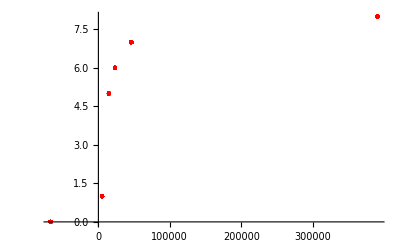

```mathematica
ListPlot[Take[variacData[[2,1]],8000],PlotStyle->Red, PlotMarkers->{Automatic,Tiny}]
```

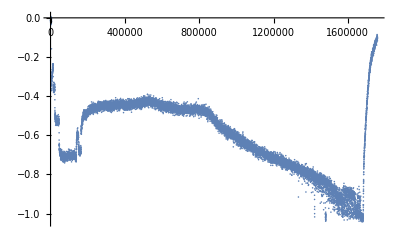

```mathematica
ListPlot[hvData[[2,3]]]
```

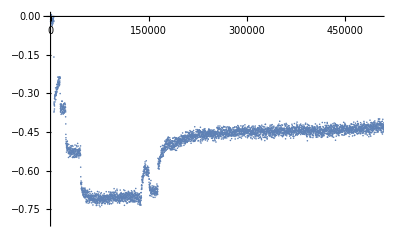

```mathematica
ListPlot[hvData[[2,3]],PlotRange->{{0,500000},{-.8,0}}]
```

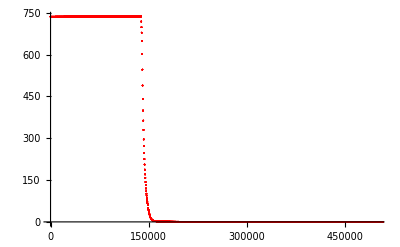

```mathematica
ListPlot[piraniData[[2,1]],PlotRange->{{0,500000},All},PlotStyle->Red]
```

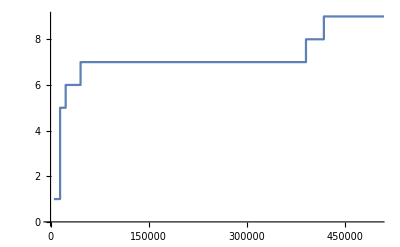

```mathematica
ListStepPlot[DeleteDuplicates[variacData[[2,1]]],PlotRange->{{0,500000},All}]
```

```mathematica
Dimensions[piraniData[[2]]]
```

{1,84605,2}

```mathematica
piraniData[[2,1,1]]
```

{6.287,736.}

```mathematica
piraniFlat=Flatten[piraniData[[2]],{{2},{1,3}}];
```

```mathematica
Export["c:\\temp\\pirani.csv",piraniFlat]
```

c:\temp\pirani.csv

```mathematica
command=GetDeviceData["Command",jfile];
```

```mathematica
command[[1]]
```

{observer,ip,text}

```mathematica
MatrixForm[command[[2,3]]]
```

(10000. | #promote: cching
64000. | RP on
445000. | #promote: cching
990000. | TMP on
1.42×10^6 | Solenoid open
1.47×10^6 | Set needle valve:5
1.58×10^6 | Set needle valve:10
1.63×10^6 | Set needle valve:15
1.66×10^6 | Set needle valve:20
1.68×10^6 | Set needle valve:25
1.69×10^6 | Set needle valve:30
1.73×10^6 | Set needle valve:35
1.76×10^6 | Set needle valve:40
1.79×10^6 | Set needle valve:45
1.83×10^6 | Set needle valve:50
1.86×10^6 | Set needle valve:55
1.88×10^6 | Set needle valve:60
1.91×10^6 | Set needle valve:65
1.94×10^6 | Set needle valve:70
1.97×10^6 | Set needle valve:75
2.×10^6 | Set needle valve:80
2.03×10^6 | Set needle valve:85
2.06×10^6 | Set needle valve:90
2.85×10^6 | Set needle valve:95
3.08×10^6 | Solenoid closed
3.19×10^6 | TMP off
3.19×10^6 | TMP off
3.22×10^6 | Set needle valve:0
3.23×10^6 | Set needle valve:0
3.464×10^6 | RP off
3.638×10^6 | stopLog)